```mathematica
{"for α=0.55"}
```

```mathematica
Clear["`*"]

Solve[(4π)/9 1/Log[1^2/Λ^2]==0.55,Λ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Λ→-0.28102},{Λ→0.28102}}

```mathematica
Solve[A/Log[1+1/(5*0.281)]==0.55,A]
```

{{A→0.295632}}

{Mine}

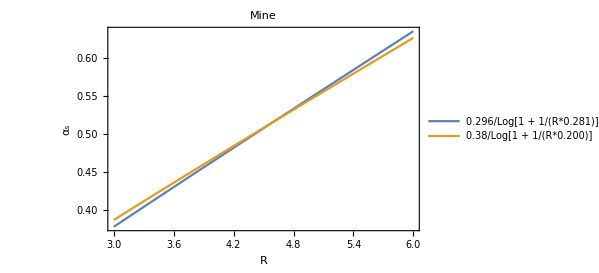

{2004 Da-Heng He}

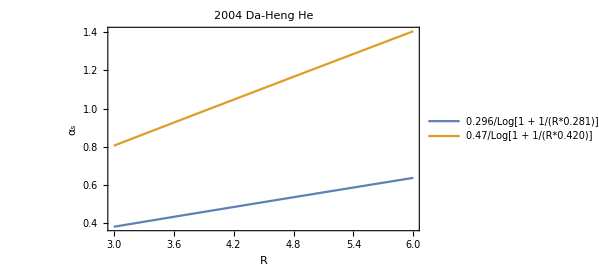

{1983 Meson baryon glueball}

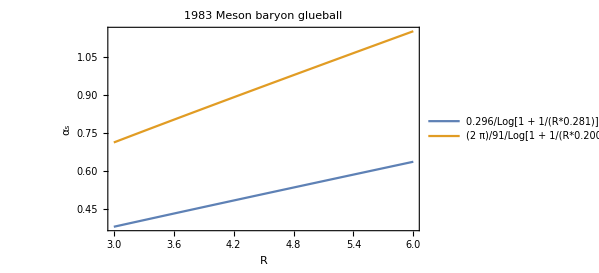

{1980 Heavy quark-antiquark}

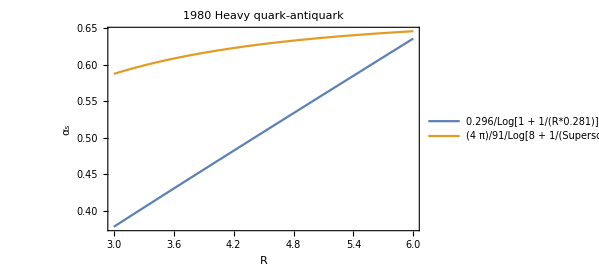

{2013 Magnetic Moment}

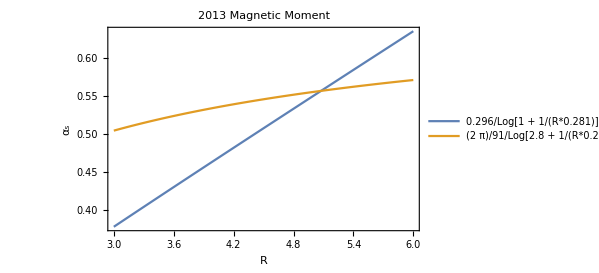

{Ebert or QCD}

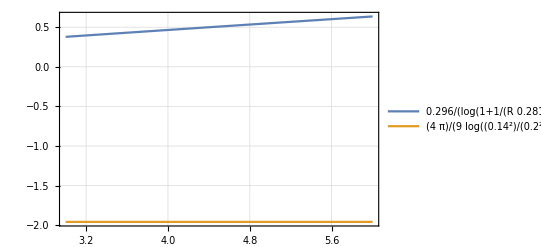

```mathematica
{"Mine"}
Plot[{0.296/Log[1+1/(R*0.281)],0.38/Log[1+1/(R*0.200)]},{R,3,6},PlotLabel->"Mine",Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Log[1 + 1/(R*0.281)]","0.38/Log[1 + 1/(R*0.200)]"},{0.75,0.3}]]
{"2004 Da-Heng He"}
Plot[{0.296/Log[1+1/(R*0.281)],0.47/Log[1+1/(R*0.420)]},{R,3,6},PlotLabel->"2004 Da-Heng He",Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Log[1 + 1/(R*0.281)]","0.47/Log[1 + 1/(R*0.420)]"},{0.75,0.5}]]
{"1983 Meson baryon glueball"}
Plot[{0.296/Log[1+1/(R*0.281)],(2π)/9 1/Log[1+1/(R*0.200)]},{R,3,6},PlotLabel->"1983 Meson baryon glueball",Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Log[1 + 1/(R*0.281)]","(2  π)/91/Log[1 + 1/(R*0.200)]"},{0.75,0.5}]]
{"1980 Heavy quark-antiquark"}
Plot[{0.296/Log[1+1/(R*0.281)],(4π)/9 1/Log[8+1/(R^2*0.200^2)]},{R,3,6},PlotLabel->"1980 Heavy quark-antiquark",Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Log[1 + 1/(R*0.281)]","(4  π)/91/Log[8 + 1/(SuperscriptBox[R, 2]*SuperscriptBox[0.200, 2])]"},{0.75,0.3}]]
{"2013 Magnetic Moment"}
Plot[{0.296/Log[1+1/(R*0.281)],(2π)/9 1/Log[2.8+1/(R*0.281)]},{R,3,6},PlotLabel->"2013 Magnetic Moment",Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Log[1 + 1/(R*0.281)]","(2  π)/91/Log[2.8 + 1/(R*0.281)]"},{0.75,0.3}]]
{"Ebert or QCD"}
Plot[{0.296/Log[1+1/(R*0.281)],(4π)/9 1/Log[0.14^2/0.200^2]},{R,3,6},PlotTheme->"Detailed"]
```